# Reproduce Figure 3(a) of Haughton and Ogden (JMPS, vol. 27, 1979, pp.489-512)

Please note that although the tube is subjected to an internal pressure P and an axial force F, rather than using these two as control parameters, Haughton and Ogden used  λa and λz as control parameters. This is why all the bifurcation results are given as λz against λa curves, for fixed mode numbers. The more standard approach in the engineering community is to plot load against the mode number, and to identify the load minimum and the associated critical mode number. The load could be P with fixed F, or F with fixed P.
In the following calculations, L/B=20, so comparison should be made with their Figure 3(a)

## Chapter 0: Specifying A, B, and material model

```mathematica
start= DateList[]
```

{2022,5,30,16,34,17.604496}

```mathematica
Neosub={W->Function[{x,y,z},1/2 (x^2+y^2+z^2-3)]};
Neosubt={W->Function[{x,y},1/2 (x^2+y^2+x^-2 y^-2-3)]};
Mooneysub={W->Function[{x,y,z},Γ (x^2+y^2+z^2-3) + (1-Γ)(x^2 y^2+x^2 z^2+z^2 y^2-3)]};
Mooneysubt={W->Function[{x,y},Γ (x^2+y^2+x^-2 y^-2-3) + (1-Γ)(x^2 y^2+x^-2+y^-2-3)]};

subenergy=Neosub;subenergyt=Neosubt;
```

## Chapter 2: The basic state and pressure

```mathematica
W1=D[W[x,y,1/(x y)],x]/.subenergy/.{x->λ, y->λz};
W2=D[W[x,y,1/(x y)],y]/.subenergy/.{x->λ, y->λz};
W11=D[W[x,y,1/(x y)],x,x]/.subenergy/.{x->λ, y->λz};
```

```mathematica
kap[λ_,λz_]=W1/(λz λ^2-1);dkap[λ_,λz_]=D[kap[λ,λz],λz]; (* used in calculating P *)
pii[λ_,λz_]=(λ(2 λz W2-λ W1))/((λz λ^2-1)^2);dpii[λ_,λz_]=D[pii[λ,λz],λz]; (* used in calculating F *)
ptem=Integrate[kap[λ,λz],λ];
```

```mathematica
λb=(√(-A^2+B^2+A^2 λa^2 λz))/(B √λz);
```

```mathematica
pressure=Simplify[(ptem/.λ->λa)-(ptem/.λ->λb)]
```

(λz Log[λa]+1/2 (-1/λa^2+(B^2 λz)/(B^2+A^2 (-1+λa^2 λz))-2 λz Log[(√(B^2+A^2 (-1+λa^2 λz)))/(B √λz)]))/λz^2

```mathematica
A=0.85;B=1; H=B-A;R=(A+B)/2;
```

## Chapter 3: The eigenvalue problem

### The moduli (to be called in The Error Function)

```mathematica
moduli:=Module[{},a=A λa;b=B λb;λ1[r_]=r/√(A^2+λz r^2-a^2 λz);
λ2[r_]=λz;
λ3[r_]=√(A^2+λz r^2-a^2 λz)/(r λz);  
σ1[r_]=λ1[r]Derivative[1,0,0][W][λ1[r],λ2[r],λ3[r]];
σ2[r_]=λ2[r]Derivative[0,1,0][W][λ1[r],λ2[r],λ3[r]];
σ3[r_]=λ3[r]Derivative[0,0,1][W][λ1[r],λ2[r],λ3[r]];B1122[r_]=λ1[r] λ2[r] Derivative[1,1,0][W][λ1[r],λ2[r],λ3[r]];
B2211[r_]=λ1[r] λ2[r] Derivative[1,1,0][W][λ1[r],λ2[r],λ3[r]];
B1133[r_]=λ1[r] λ3[r] Derivative[1,0,1][W][λ1[r],λ2[r],λ3[r]];
B3311[r_]=λ1[r] λ3[r] Derivative[1,0,1][W][λ1[r],λ2[r],λ3[r]];
B2233[r_]=λ2[r] λ3[r] Derivative[0,1,1][W][λ1[r],λ2[r],λ3[r]];
B3322[r_]=λ2[r] λ3[r] Derivative[0,1,1][W][λ1[r],λ2[r],λ3[r]];
B1111[r_]=λ1[r] λ1[r] Derivative[2,0,0][W][λ1[r],λ2[r],λ3[r]];
B2222[r_]=λ2[r] λ2[r] Derivative[0,2,0][W][λ1[r],λ2[r],λ3[r]];
B3333[r_]=λ3[r] λ3[r] Derivative[0,0,2][W][λ1[r],λ2[r],λ3[r]];
B1212[r_]=(σ1[r]-σ2[r])/(λ1[r]^2 -λ2[r]^2)λ1[r]^2;
B1313[r_]=(σ1[r]-σ3[r])/(λ1[r]^2 -λ3[r]^2)λ1[r]^2;
B2323[r_]=(σ2[r]-σ3[r])/(λ2[r]^2 -λ3[r]^2)λ2[r]^2;
B2121[r_]=(σ1[r]-σ2[r])/(λ1[r]^2 -λ2[r]^2)λ2[r]^2;
B3131[r_]=(σ1[r]-σ3[r])/(λ1[r]^2 -λ3[r]^2)λ3[r]^2;
B3232[r_]=(σ3[r]-σ2[r])/(λ3[r]^2 -λ2[r]^2)λ3[r]^2;
B1221[r_]=B1212[r]-σ1[r];
B3113[r_]=B3131[r]-σ3[r];
B3223[r_]=B2323[r]-σ2[r];
B2112[r_]=B1212[r]-σ1[r];
B1331[r_]=B3131[r]-σ3[r];
B2332[r_]=B2323[r]-σ2[r];
σ33[r_]=((ptem/.{λ->λb})-ptem)/.λ->(r/(√(r^2 λz-(A λa)^2 λz+A^2)));
p1[r_]=σ3[r]-σ33[r];
σ33first[r_]=(σ1[r]-σ3[r])/r; (* 1st derivative of σ33 *) ];
```

### The matrix A (to be called in The Error Function)

```mathematica
(* eqn=r^4*D[B3232[r] f^(3)[r]+(r B3232'[r]+2 B3232[r])*f^(2)[r]/r+(r B3232'[r]- B3232[r]) f^(1)[r]/r^2-(r B3232'[r]- B3232[r]) f[r]/r^3,r]+α^2 r^2 ((2 B2233[r]+2 B3223[r]-B3333[r]-B2222[r]) r^2 f^(2)[r]+(2 r B3223'[r]+2 r B2233'[r]-r B3333'[r]-r B2222'[r]-B3333[r]-B2222[r]+2 B2233[r]+2 B3223[r]) r f^(1)[r]+(r^2 B3223''[r]+r^2 p1''[r]+r B3223'[r]+r B1122'[r]-r B1133'[r]-r B2222'[r]+r B2233'[r]+B1111[r]+B2222[r]-2 B1122[r]-2 B3223[r]) f[r])+α^4 r^4 B2323[r] f[r];
ttt= f^(4)[r]/.Solve[eqn==0, f^(4)[r]][[1]];
a31=Coefficient[ttt, f[r]] ;
a32=Coefficient[ttt, f'[r]] ;
a33=Coefficient[ttt, f''[r]] ;
a34=Coefficient[ttt, f^(3)[r]] ;*)
```

```mathematica
matrixAA:=Module[{},LB=20;α=2 Pi/(λz LB);  (* note that this has corrected an error in Haughton & Ogden's eqn (61) *)
a31=-1/(r^4 B3232[r])(r^2 α^2 B1111[r]-2 r^2 α^2 B1122[r]+r^2 α^2 B2222[r]+r^4 α^4 B2323[r]-2 r^2 α^2 B3223[r]-3 B3232[r]+r^3 α^2 B1122'[r]-r^3 α^2 B1133'[r]-r^3 α^2 B2222'[r]+r^3 α^2 B2233'[r]+r^3 α^2 B3223'[r]+3 r B3232'[r]+r^4 α^2 B3223''[r]-r^2 B3232''[r]+r^4 α^2 p1''[r]);
a32=1/(r^3 B3232[r])(r^2 α^2 B2222[r]-2 r^2 α^2 B2233[r]-2 r^2 α^2 B3223[r]-3 B3232[r]+r^2 α^2 B3333[r]+r^3 α^2 B2222'[r]-2 r^3 α^2 B2233'[r]-2 r^3 α^2 B3223'[r]+3 r B3232'[r]+r^3 α^2 B3333'[r]-r^2 B3232''[r]);
a33=-(-r^2 α^2 B2222[r]+2 r^2 α^2 B2233[r]+2 r^2 α^2 B3223[r]-3 B3232[r]-r^2 α^2 B3333[r]+3 r B3232'[r]+r^2 B3232''[r])/(r^2 B3232[r]);
a34=-2 (1/r+B3232'[r]/B3232[r]);

s31=a31/.subenergy;
s32=a32/.subenergy;
s33=a33/.subenergy;
s34=a34/.subenergy;

matrixA=({{0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}, {s31, s32, s33, s34}})  (* y'-A y=0 *)];
```

### Evans function (to be called in The Error Function)

```mathematica
(*mb11[r_]=α^2 r^2-1;
mb21[r_]=-(r B3232'[r]-B3232[r])+α^2 r^2(r B3232'[r]-r σ33first[r]+B3232[r]-σ3[r]+B1122[r]-B2222[r]+B2233[r]-B1133[r] );
 mb22[r_]=(r B3232'[r]-B3232[r])r-α^2 r^3(B3333[r]+B2222[r]-2 B2233[r]-B3223[r]+σ3[r]);
mb23[r_]=r^2(r B3232'[r]+2B3232[r]);
MB[r_]=({{mb11[r], r, r^2, 0}, {mb21[r], mb22[r], mb23[r], B3232[r] r^3}});

BConditions=MB[r].{f[r],f'[r],f''[r],f'''[r]};
subfff=Solve[BConditions=={0,0},{f[r], f'''[r]}][[1]];
yx3r=Simplify[{f[r],f'[r],f''[r],f'''[r]}/.subfff/.{f'[r]->1,f''[r]->0 }];
yx4r=Simplify[{f[r],f'[r],f''[r],f'''[r]}/.subfff/.{f'[r]->0,f''[r]->1 }];*)
```

```mathematica
ind={{1,2},{1,3},{1,4},{2,3},{2,4},{3,4}};
```

```mathematica
evansF:=Module[{},mb11[r_]=α^2 r^2-1;
mb21[r_]=-(r B3232'[r]-B3232[r])+α^2 r^2(r B3232'[r]-r σ33first[r]+B3232[r]-σ3[r]+B1122[r]-B2222[r]+B2233[r]-B1133[r] );
 mb22[r_]=(r B3232'[r]-B3232[r])r-α^2 r^3(B3333[r]+B2222[r]-2 B2233[r]-B3223[r]+σ3[r]);
mb23[r_]=r^2(r B3232'[r]+2B3232[r]);
MB[r_]=({{mb11[r], r, r^2, 0}, {mb21[r], mb22[r], mb23[r], B3232[r] r^3}});
MAA=MB[A λa]/.subenergy;
MBB=MB[B λb]/.subenergy;

yx3r={r/(1-r^2 α^2),1,0,1/((-1+r^2 α^2) B3232[r])α^2 (B1122[r]-B1133[r]-2 B2222[r]+r^2 α^2 B2222[r]+3 B2233[r]-2 r^2 α^2 B2233[r]+B3223[r]-r^2 α^2 B3223[r]+2 B3232[r]-B3333[r]+r^2 α^2 B3333[r]-2 σ3[r]+r^2 α^2 σ3[r]-r σ33first[r])};
yx4r={r^2/(1-r^2 α^2),0,1,-1/(r (-1+r^2 α^2) B3232[r])(-r^2 α^2 B1122[r]+r^2 α^2 B1133[r]+r^2 α^2 B2222[r]-r^2 α^2 B2233[r]-3 B3232[r]+r^2 α^2 B3232[r]+r^2 α^2 σ3[r]+r^3 α^2 σ33first[r])};

yx3[r_]=yx3r/.subenergy;
yx4[r_]=yx4r/.subenergy;
ϕϕa=Array[ϕ,6];Do[ϕ[p]=0,
{p,1,6}];ϕϕb=Array[ϕ,6];Do[ϕ[p]=0,
{p,1,6}];
MM0={yx3[a],yx4[a]}; 
BCa=Transpose[MM0];
MM1={yx3[b],yx4[b]};
BCb=Transpose[MM1]
];
```

### The error function

Two different error functions are defined here. 
err1 shoots from both ends and matches at point d=(a+b)/2
err2 is based on the determinant method
The last command selects which error function to use

```mathematica
err1[k_]:=Module[{},λa=k; moduli; d=(a+b)/2;matrixAA; evansF; AA0=matrixA;Do[i=ind[[p,1]];j=ind[[p,2]];
 ϕϕa[[p]]=Det[{BCa[[i]],BCa[[j]]}];
ϕϕb[[p]]=Det[{BCb[[i]],BCb[[j]]}],{p,1,6}];
mf0=Array[f0,{6,6}];Do[f0[p,q]=0,
{p,1,6},{q,1,6}];
Do[i=ind[[p,1]];j=ind[[p,2]];ii=ind[[q,1]];jj=ind[[q,2]]; If[(i==ii)&&(j==jj),mf0[[p,q]]=AA0[[i,i]]+AA0[[j,j]]];If[(i==ii)&&(j≠jj),mf0[[p,q]]=AA0[[j,jj]]];If[(j==jj)&&(i≠ii),mf0[[p,q]]=AA0[[i,ii]]];If[(j==ii)&&(i!=jj),mf0[[p,q]]=-AA0[[i,jj]]];
If[(i==jj)&&(j≠ii),mf0[[p,q]]=-AA0[[j,ii]]];
If[(i≠ii)&&(j≠ii)&&(i≠jj)&&(j≠jj),mf0[[p,q]]=0],
{p,1,6},{q,1,6}];
sol1=NDSolve[{ϕϕ'[r]-mf0.ϕϕ[r]==0,ϕϕ[a]==ϕϕa},ϕϕ,{r,a,b},WorkingPrecision->MachinePrecision][[1]];
ϕϕLeft=ϕϕ[d]/.sol1;
sol2=NDSolve[{ϕϕ'[r]-mf0.ϕϕ[r]==0,ϕϕ[b]==ϕϕb},ϕϕ,{r,a,b},WorkingPrecision->MachinePrecision][[1]];
ϕϕRight=ϕϕ[d]/.sol2;
N1=ϕϕLeft[[1]]*ϕϕRight[[6]]-ϕϕLeft[[2]]*ϕϕRight[[5]]+ϕϕLeft[[3]]*ϕϕRight[[4]]+ϕϕLeft[[4]]*ϕϕRight[[3]]-ϕϕLeft[[5]]*ϕϕRight[[2]]+ϕϕLeft[[6]]*ϕϕRight[[1]]
]
```

```mathematica
err2[k_]:=Module[{},λa=k; moduli;matrixAA; evansF; AA0=matrixA;
sol1=NDSolve[{yy'[r]-AA0.yy[r]==0,yy[a]==yx3[a]},yy,{r,a,b},WorkingPrecision->MachinePrecision][[1]];
yyr1=yy[b]/.sol1;
sol2=NDSolve[{yy'[r]-AA0.yy[r]==0,yy[a]==yx4[a]},yy,{r,a,b},WorkingPrecision->MachinePrecision][[1]];
yyr2=yy[b]/.sol2;bbcc=(MB[b]/.subenergy).Transpose[{yyr1,yyr2}];
N1=Det[bbcc]
]
```

```mathematica
err[kk_]:=err1[kk]
```

### The root-finding command

```mathematica
froot[s0_, s1_]:=Module[{u0,u1, v0,v1},u0=s0; u1=s1; v0=err[u0]; v1=err[u1];Do[u2=(u1 v0-u0 v1)/(v0-v1);u0=u1;v0=v1;u1=u2;v1=err[u1];If[k==150, Print["No solution found    ",u1]];If[Abs[1-u1/u0]<10^(-6), Break[]],{k,1,150}]; u1];
```

## Chapter 4: Calculations for the first bifurcation point

#### We first compute the bifurcation value of λa when λz=0.30. The following plot shows roughly where it is

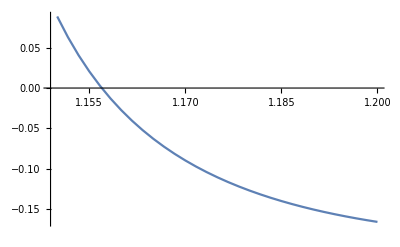

```mathematica
λz=0.30;nn=30;begin=1.15; end=1.2;step=(end-begin)/nn;res4=Table[N[{begin+step*kk,err[begin+step*kk]},6],{kk,0,nn}];ListPlot[{res4},Joined->True]
```

```mathematica
froot[1.15,1.2]
```

1.15696

```mathematica
result={{0.3,1.1569568464233753 }}; results={{0.3,0.3*1.1569568464233753^2 }};
```

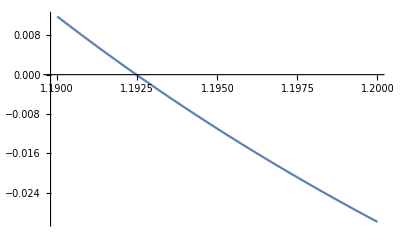

```mathematica
λz=0.302;nn=30;begin=1.19; end=1.2;step=(end-begin)/nn;res4=Table[N[{begin+step*kk,err[begin+step*kk]},6],{kk,0,nn}];ListPlot[{res4},Joined->True]
```

```mathematica
guess=froot[1.19,1.2]
```

1.19247

```mathematica
result=Append[result,{λz,guess}];results=Append[results,{λz,λz*guess^2}]
```

{{0.3,0.401565},{0.302,0.429442}}

#### Once one bifurcation point is identified, it is continued in the (λz, λa) plane using a DO loop.

### neo-Hookean left branch

```mathematica
scale=101/100;Do[λz=λz+0.0005; If[Abs[λz]>5, Break[]];guess1:=scale*guess;guessT=froot[guess, guess1]; scale=guessT/guess;guess=guessT;result=Append[result,{λz,guess}];results=Append[results,{λz,λz*guess^2}],{k,1,200}]
```

### neo-Hookean right branch

```mathematica
Do[λz=λz*102/100; If[Abs[λz]>5, Break[]];guessT=froot[guess, guess1]; scale=guessT/guess;guess=guessT;result=Append[result,{λz,guess}],{k,0,400}]
```

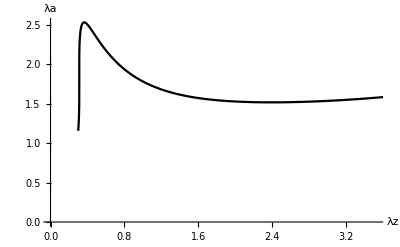

```mathematica
fig1a=ListPlot[result, Joined->True, PlotStyle->{Black}, AxesStyle->{Directive[Black,10],Directive[Black,10]}, AxesLabel->{Style["λz",FontSize->18,FontFamily->"Times New Roman"],Style["λa",FontSize->18,FontFamily->"Times New Roman"]}]
```

#### The curve corresponding to P=0 when A=0.85

```mathematica
(pressure/.{λa->(a/A),λz->λ})
```

0.0318822

```mathematica
(* The following is the equation corresponding to P =0. It is solved to express λ as a function of a *)
```

```mathematica
flam[a_]:=λ/.FindRoot[(λ Log[a/A]+1/2 (-A^2/a^2+(B^2 λ)/(-A^2+B^2+a^2 λ)-2 λ Log[(√(-A^2+B^2+a^2 λ))/(B √λ)]))/λ^2==0,{λ,guess}];
```

```mathematica
A=0.85;guess=4.5;guess=flam[0.4]
```

4.51563

```mathematica
data={{guess, 0.4/A}};  (* this is (λz, λa), where  λa=a/A *)
Do[at=0.4+0.01*j; guess=flam[at];data=Append[data,{guess, at/A}], {j,1,500}];
```

```mathematica
f1=Interpolation[data];f2=Interpolation[result]; (* Subscript[λ, z]=f1[Subscript[λ, a]] is the solution of P=0, whereas Subscript[λ, z]=f2[Subscript[λ, a]] is the solution of the bifurcation condition *)
```

```mathematica
xx=x/.FindRoot[f1[x]==f2[x],{x,0.31}]  (* This gives the intersection point of the two curves *)
```

0.311228

```mathematica
f1[xx]  (* value of λa where the two curves intersect*)
```

1.79251

```mathematica
a=f1[xx] A
```

1.52363

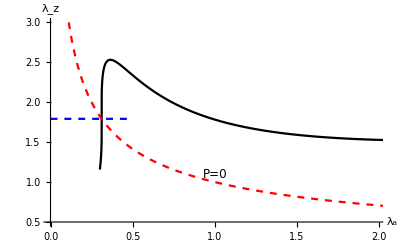

```mathematica
ListPlot[{result,data,{{0, 1.79250573},{0.5, 1.79250573}}},Joined->True, PlotRange->{0.5,3},PlotStyle->{{ Black},{Dashed,Red},{Blue,Dashed}},AxesLabel->{Style["λ_a",FontSize->18,FontColor->Black,FontFamily->"Cambria Math"],Style["λ_z",FontSize->18,FontColor->Black,FontFamily->"Cambria"]},AxesStyle->Black,TicksStyle->Directive[Black,14],Epilog->{Text[Style["P=0",FontSize->12,FontFamily->"Cambria Math"],{1,1.1}],Text[Style["",FontSize->12,FontFamily->"Cambria Math"],{3.515,0.328}] }]
```

```mathematica
(* This figure seems to have reproduced part of Haughton and Ogden's Fig. 3a *)
```

```mathematica
end=Print["end",DateList[]]
```

end{2022,5,30,16,35,52.9773505}

```mathematica
start
```

{2022,5,30,16,34,17.604496}